# Non-Trivial Application

### Initialize Landscape

```mathematica
landscape[x_,y_]:=A Sin[x]+B Cos[y]-c*Exp[-((x-x0)^2+(y-y0)^2)]+d(x^2+y^2)

(*Parameters*)
A=2;
B=1;
c=8;
d=0.1;
x0=2;
y0=1;

(*Plot the function*)
land=Plot3D[landscape[x,y],{x,-6,6},{y,-6,6},PlotRange->All,AxesLabel->{"X","Y","Z"},MeshFunctions->{#3&},MeshStyle->{{Thick,Transparent}},ClippingStyle->None,ColorFunction->"DeepSeaColors",PlotStyle->Opacity[0.5],Background->White,Boxed->False,ImageSize->Medium]
```

-Graphics3D-

#### Mathematica’s FindMinimum

```mathematica
mathematicaMin=FindMinimum[{landscape[x,y],-5<=x<=5,-5<=y<=5},{{x,0},{y,0}}];
mathematicaPlot=Graphics3D[{Opacity[1],White,Ellipsoid[{-1.42755,-2.59574,-1.95662},{0.2,0.2,0.7}]}];
Show[land,mathematicaPlot,ImageSize->Medium]
```

-Graphics3D-

#### Generate Contour Plot

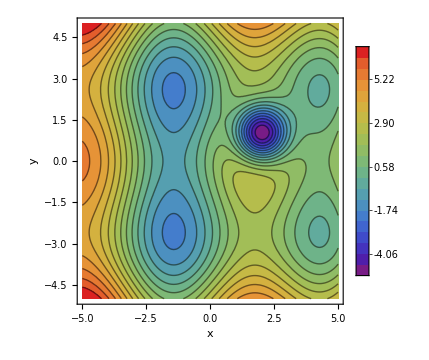

```mathematica
ContourPlot[landscape[x,y],{x,-5,5},{y,-5,5},Contours->20,ColorFunction->"Rainbow",PlotLegends->Automatic,FrameLabel->{"x","y"},ImageSize->Medium]
```

#### Random Sampling

```mathematica
randomX=RandomReal[{-6,6},100];
randomY=RandomReal[{-6,6},100];
```

#### Randomly Distributed Starting Points for GD

```mathematica
arrows=Graphics3D[Table[{RGBColor[0,0.3,0.7,0.7],Arrowheads[0.020],Arrow[Tube[{{randomX[[i]],randomY[[i]],landscape[randomX[[i]],randomY[[i]]]+3},{randomX[[i]],randomY[[i]],landscape[randomX[[i]],randomY[[i]]]}},0]]},{i,1,Length[randomX]}],Axes->True,AxesLabel->{"X","Y","Z"},Background->White,Boxed->False,ImageSize->Medium];
```

```mathematica
startArrow=Graphics3D[{Cyan,Arrowheads[0.020],Arrow[Tube[{{1.046037,2.030149,0.694834},{1.046037,2.030149,0.694833}},0]]},Axes->True,AxesLabel->{"X","Y","Z"},Background->White,Boxed->False,ImageSize->Medium];
```

#### Create Path

```mathematica
(*I admit this is not very readable*)
data={{1.0460370766269353,2.0301493830323727,0.6948330588789954},{1.091232515466363,1.9409452782607224,0.46330539266360554},{1.1476247520503504,1.8583624976520774,0.16530421740897538},{1.2106874123601497,1.7807538584767195,-0.20530657520824747},{1.2778130550403788,1.7066313376428581,-0.6483216987037655},{1.3475322806931778,1.6349429175572257,-1.157204730054003},{1.4189918921167912,1.5649891904571906,-1.719053269577405},{1.4916796503719956,1.4963124855287147,-2.3148528704617837},{1.5652831969006253,1.4286181878485715,-2.920242261554004},{1.6396173974705452,1.3617270327858062,-3.506880638213372},{1.7145891773205257,1.2955512651202472,-4.044386846538755},{1.790188413364947,1.2300932212333429,-4.50271081567021},{1.866510074910595,1.1654789505270076,-4.854709358128114},{1.9438542267323353,1.1020921839351108,-5.078649907684929},{2.02323037064199,1.0412692624495903,-5.1604107533737515},{2.123146695635361,1.0371792746966753,-5.099122552703846},{2.02328214913516,1.0423823845656985,-5.1604016922605},{2.120982102611686,1.0210582411905333,-5.098832902101802},{2.023883821130519,1.0449731681902974,-5.160350373572845},{2.1061884276039877,0.9881757056303608,-5.09758943078422},{2.0266840847618113,1.0488309565921174,-5.160190977410435},{2.06436314257576,0.9562011093383671,-5.096142327360105},{2.0296826081693538,1.0499948219916473,-5.160122994108132},{2.0344247321121722,0.9501073239725711,-5.096033069770379},{2.030109983350014,1.0500141953234419,-5.160121814689952},{2.0304784504011733,0.9500148741655849,-5.096032109891008},{2.0301431330578965,1.050014311975401,-5.160121807827785},{2.0301726457753007,0.9500143163304036,-5.09603210212482},{2.030145698899409,1.0500143126997328,-5.160121807803629},{2.030148974922852,0.9500143127533944,-5.096032101921841},{2.030145897701288,1.050014312706048,-5.160121807804797},{2.0301471410305743,0.9500143127137772,-5.096032101908506},{2.0301459131808546,1.0500143127062391,-5.160121807804905},{2.030146999271156,0.9500143127121371,-5.096032101907491},{2.0301459142964524,1.0500143127062513,-5.160121807804914},{2.030146988340218,0.9500143127120192,-5.0960321019074115},{2.030145914432858,1.050014312706253,-5.160121807804915},{2.0301469878425884,0.950014312712014,-5.096032101907409},{2.0301459143729192,1.0500143127062522,-5.160121807804915},{2.030146987782657,0.9500143127120133,-5.096032101907408},{2.030145914375515,1.0500143127062522,-5.160121807804914},{2.0301469884192804,0.9500143127120201,-5.096032101907413},{2.0301459143243377,1.0500143127062518,-5.160121807804914},{2.030146988368103,0.9500143127120196,-5.096032101907412},{2.0301459143356877,1.050014312706252,-5.160121807804915},{2.030146987111383,0.9500143127120062,-5.0960321019074035},{2.030145914392042,1.0500143127062527,-5.160121807804915},{2.0301469878017797,0.9500143127120138,-5.096032101907409},{2.0301459143321114,1.050014312706252,-5.160121807804914},{2.0301469883758703,0.9500143127120199,-5.096032101907413},{2.0301459142809275,1.0500143127062516,-5.160121807804914},{2.0301469883246863,0.9500143127120194,-5.096032101907413},{2.030145914292271,1.0500143127062518,-5.160121807804913},{2.0301469896040927,0.9500143127120333,-5.096032101907422},{2.0301459143836578,1.050014312706253,-5.160121807804915},{2.030146987793388,0.950014312712014,-5.09603210190741},{2.030145914323719,1.0500143127062522,-5.160121807804915},{2.030146988367471,0.9500143127120201,-5.096032101907413},{2.030145914397584,1.0500143127062531,-5.160121807804915},{2.0301469871732865,0.9500143127120073,-5.096032101907405},{2.0301459142663627,1.0500143127062516,-5.160121807804913},{2.0301469889441566,0.9500143127120262,-5.096032101907417},{2.0301459143489953,1.0500143127062525,-5.160121807804915},{2.0301469877587257,0.9500143127120135,-5.096032101907409},{2.0301459143515848,1.0500143127062525,-5.160121807804914},{2.0301469883953502,0.9500143127120203,-5.096032101907413},{2.0301459143004084,1.050014312706252,-5.160121807804913},{2.0301469889782022,0.9500143127120266,-5.096032101907417},{2.0301459143830414,1.050014312706253,-5.160121807804913},{2.030146988426807,0.9500143127120207,-5.096032101907414},{2.0301459143318636,1.0500143127062525,-5.160121807804914},{2.030146987741594,0.9500143127120135,-5.09603210190741},{2.0301459143344522,1.0500143127062525,-5.160121807804914},{2.0301469883782177,0.9500143127120203,-5.096032101907414},{2.030145914283275,1.050014312706252,-5.160121807804914},{2.0301469883270338,0.9500143127120199,-5.096032101907413},{2.0301459143571465,1.050014312706253,-5.160121807804914},{2.030146987766877,0.950014312712014,-5.09603210190741},{2.030145914359735,1.050014312706253,-5.160121807804914},{2.0301469884035006,0.9500143127120207,-5.096032101907414},{2.030145914308558,1.0500143127062525,-5.160121807804913},{2.0301469889863517,0.9500143127120271,-5.096032101907419},{2.0301459143286626,1.0500143127062527,-5.160121807804915},{2.0301469877383864,0.9500143127120138,-5.096032101907409},{2.0301459143312455,1.0500143127062527,-5.160121807804914},{2.030146988375011,0.9500143127120205,-5.096032101907413},{2.0301459144051237,1.0500143127062536,-5.160121807804915},{2.030146987180826,0.9500143127120078,-5.096032101907406},{2.03014591433643,1.050014312706253,-5.160121807804913},{2.0301469890142307,0.9500143127120275,-5.096032101907419},{2.0301459142940144,1.0500143127062525,-5.160121807804914},{2.03014698833778,0.9500143127120203,-5.096032101907414},{2.0301459143053644,1.0500143127062527,-5.160121807804913},{2.03014698834913,0.9500143127120205,-5.096032101907414},{2.0301459143167144,1.050014312706253,-5.160121807804914},{2.03014698836048,0.9500143127120207,-5.096032101907413},{2.03014591445312,1.0500143127062544,-5.160121807804915},{2.030146987228829,0.9500143127120086,-5.096032101907406},{2.0301459143844345,1.0500143127062538,-5.160121807804914},{2.030146987794172,0.9500143127120149,-5.09603210190741}};
```

```mathematica
(*make a path of ellipsoids (resembling points) by reading from the data*)
path=Graphics3D[Table[{Opacity[0.8],Cyan,Ellipsoid[point,{0.08,0.08,0.2}]},{point,data}]];
```

#### Surface with randomized starting points, one optimal path, and one good starting point

```mathematica
(* overlay the surface, a sample path, the start arrow (teal, slightly different), and the randomly sampled arrows (navy) *)
Show[land,arrows,startArrow,path,BoxRatios->{1,1,0.5},ImageSize->Medium]
```

Show::gcomb: Could not combine the graphics objects in Show[land,arrows,startArrow,path,BoxRatios→{1,1,0.5},ImageSize→Medium].

Show[land,arrows,startArrow,path,BoxRatios→{1,1,0.5},ImageSize→Medium]